# Computation of the Virtual contribution to the R - ratio

```mathematica
Quit[]
```

## Resources

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Import[NotebookDirectory[]<>"FeynCalc/FeynCalc.m"]
$FAVerbose=0;
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

## Born

```mathematica
diags=InsertFields[CreateTopologies[0,1->2],{V[1]}->{F[3,{1}],-F[3,{1}]},InsertionLevel->{Classes},Model->"SMQCD"];
bornfcamp=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,Contract->True,DropSumOver->True,Prefactor->3/2 SMP["e_Q"],FinalSubstitutions->{SMP["m_u"]->0},LorentzIndexNames->{μ, ν, σ},SUNFIndexNames->{_,m,n}];
FCClearScalarProducts[];
ScalarProduct[k1]=SMP["m_q"]^2;
ScalarProduct[k2]=SMP["m_q"]^2;
ScalarProduct[k1,k2]=s/2 ;
ampsq=(bornfcamp (ComplexConjugate[bornfcamp]))//SUNSimplify[#,SUNNToCACF->False]&//DoPolarizationSums[#,p,0,VirtualBoson->True]&//FermionSpinSum//DiracSimplify//FeynAmpDenominatorExplicit//Simplify;
ampsq//ReplaceAll[#,{SMP["m_q"]->0,x3->2-x1-x2,SMP["e"]^2->(4 Pi SMP["alpha_fs"]),SMP["g_s"]^2->(4 Pi SMP["alpha_s"])}]&//Simplify;
BornMassless=ampsq/.{SMP["m_q"]->0,SUNN->3,SMP["e"]^2 -> (4 Pi SMP["alpha_fs"]),D->4-2Epsilon}
```

24 π α (2-2 ε) s e_Q^2

```mathematica
bornfcamp
```

e e_Q δ_mn (φ(k1)).(γ·ε(p)).(φ(-k2))

```mathematica
BornMassless4D=BornMassless/.{Epsilon->0}
```

48 π α s e_Q^2

```mathematica
FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{SMP["m_u"]->0},LorentzIndexNames->{μ, ν, σ},SUNFIndexNames->{_,m,n}]
```

2/3 e δ_mn (φ(k1)).(γ·ε(p)).(φ(-k2))

## Generate the diagram

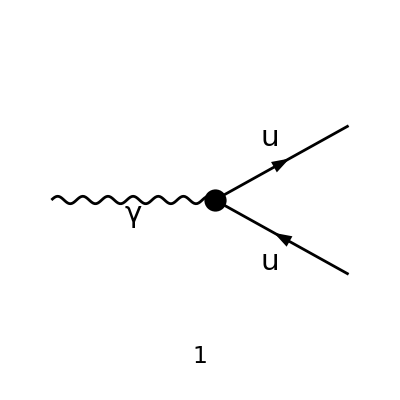

```mathematica
BornDiag=InsertFields[CreateTopologies[
0,
1->2,
ExcludeTopologies->{Tadpoles,WFCorrections}],
{V[1]}
->{F[3,{1}],-F[3,{1}]},
InsertionLevel->{Particles},
ExcludeParticles->{S[_],V[2|3],(S|U)[_],F[4],F[2,{2|3}]},
Model->"SMQCD"
];
Paint[BornDiag,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
vdiags=InsertFields[CreateTopologies[
1,
1->2,
ExcludeTopologies->{Tadpoles,WFCorrections}],
{V[1]}
->{F[3,{1}],-F[3,{1}]},
InsertionLevel->{Particles},
ExcludeParticles->{S[_],V[2|3],(S|U)[_],F[4],F[2,{2|3}]},
Model->"SMQCD"
];
(* Select the vertex correction involving the gluon *)
vdiags=DiagramDelete[vdiags,1];
```

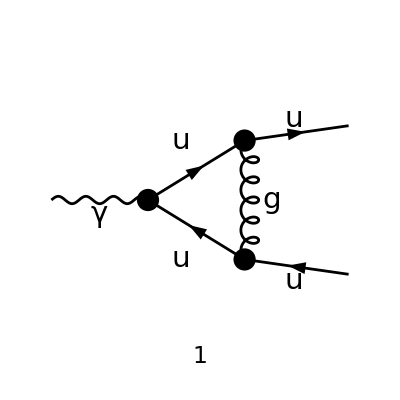

```mathematica
Paint[vdiags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

## Create the amplitudes

The index “[0]” of the amp object labels the processing step

```mathematica
Options[FCFAConvert]
```

{ChangeDimension→False,Contract→False,DropSumOver→False,FCFADiracChainJoin→True,FeynAmpDenominatorCombine→True,FinalSubstitutions→{},IncomingMomenta→{},InitialSubstitutions→{},List→True,LoopMomenta→{},LorentzIndexNames→{},OutgoingMomenta→{},Prefactor→1,SMP→False,SUNFIndexNames→{},SUNIndexNames→{},TransversePolarizationVectors→{},UndoChiralSplittings→False}

```mathematica
amp[0]=FCFAConvert[
CreateFeynAmp[diags,PreFactor->1,Truncated->False],
IncomingMomenta->{p+q},OutgoingMomenta->{p,q},LorentzIndexNames->{μ, ν, σ},SUNIndexNames->{_,_,_,a},SUNFIndexNames->{_,m,n,o},
LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{SMP["m_e"]->0,SMP["m_u"]->0},DropSumOver->True
]/.{Pair[__,Momentum[Polarization[__],_]]:>1}
```

-(ⅈ g^νσ (φ(p)).(-ⅈ γ^ν g_s T_mo^a).(γ·l).(-2/3 ⅈ e γ^μ).(γ·(l-p-q)).(-ⅈ γ^σ g_s T_on^a).(φ(-q)))/(l^2.(l-p)^2.(l-p-q)^2)

```mathematica
bornamp[0]=FCFAConvert[
CreateFeynAmp[BornDiag,PreFactor->1,Truncated->False],
IncomingMomenta->{p+q},OutgoingMomenta->{p,q},LorentzIndexNames->{μ, ν, σ},SUNIndexNames->{_,_,_,a},SUNFIndexNames->{_,m,n,o},
LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{SMP["m_e"]->0,SMP["m_u"]->0},DropSumOver->True
]/.{Pair[__,Momentum[Polarization[__],_]]:>1}
```

-(φ(p)).(-2/3 ⅈ e γ^μ δ_mn).(φ(-q))

## Process the amplitude

Define scalar products

```mathematica
FCClearScalarProducts[];
ScalarProduct[p,p]=0;
ScalarProduct[q,q]=0;
ScalarProduct[p,q]=s/2;
```

```mathematica
bornamp[1]=DiracSimplify[bornamp[0]]
```

2/3 ⅈ e δ_mn (φ(p)).γ^μ.(φ(-q))

```mathematica
amp[1]=DiracSimplify[amp[0]]
```

-(4 D (φ(p)).(γ·l).(φ(-q)) l^μ e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)+(8 (φ(p)).(γ·l).(φ(-q)) l^μ e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)+(4 D (φ(p)).(γ·l).(φ(-q)) p^μ e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)-(16 (φ(p)).(γ·l).(φ(-q)) p^μ e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)+(8 (φ(p)).(γ·l).(φ(-q)) q^μ e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)+(2 D (φ(p)).γ^μ.(φ(-q)) l^2 e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)-(4 (φ(p)).γ^μ.(φ(-q)) l^2 e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)-(4 D (φ(p)).γ^μ.(φ(-q)) (l·p) e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)+(16 (φ(p)).γ^μ.(φ(-q)) (l·p) e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)-(8 (φ(p)).γ^μ.(φ(-q)) (l·q) e g_s^2 T_mo^a T_on^a)/(3 l^2.(l-p)^2.(l-p-q)^2)

```mathematica
amp[1]=SUNSimplify[amp[1]]
```

1/(3 l^2.(l-p)^2.(l-p-q)^2)2 e C_F g_s^2 δ_mn (D l^2 (φ(p)).γ^μ.(φ(-q))-2 D (l·p) (φ(p)).γ^μ.(φ(-q))-2 D l^μ (φ(p)).(γ·l).(φ(-q))+2 D p^μ (φ(p)).(γ·l).(φ(-q))-2 l^2 (φ(p)).γ^μ.(φ(-q))+8 (l·p) (φ(p)).γ^μ.(φ(-q))-4 (l·q) (φ(p)).γ^μ.(φ(-q))+4 l^μ (φ(p)).(γ·l).(φ(-q))-8 p^μ (φ(p)).(γ·l).(φ(-q))+4 q^μ (φ(p)).(γ·l).(φ(-q)))

We are now ready to evaluate the loop integral using the techniques we saw during the course!

## Integral reduction

Let us first reproduce what we saw during the lecture

```mathematica
Rank1Triangle=FVD[l,μ] FAD[{l,0},{l+p1,0},{l+p2,0}]
```

l^μ/(l^2.(l+p1)^2.(l+p2)^2)

```mathematica
Rank1Triangle=(Dot[GSD[l],GAD[μ],GSD[p]]) FAD[{l,0},{l+p1,0},{l+p2,0}]
```

((γ·l).γ^μ.(γ·p))/(l^2.(l+p1)^2.(l+p2)^2)

FeynCalc offers a Passarino-Veltman reduction implementation (the 1/ⅈπ^2prefactor is conventional in the definition of the one-loop master integrals C_i)
Notice that the position of  the argument of the kinematics is different in the two C_1, with convention C_1(p_1^2,p_2^2,p_3^2,m_1^2,m_2^2,m_3^2)

```mathematica
TID[1/(ⅈ π^2)Rank1Triangle,l,UsePaVeBasis->True,PaVeAutoReduce->False]
```

(γ·p1).γ^μ.(γ·p) C_1(p1^2,-2 (p1·p2)+p1^2+p2^2,p2^2,0,0,0)+(γ·p2).γ^μ.(γ·p) C_1(p2^2,-2 (p1·p2)+p1^2+p2^2,p1^2,0,0,0)

We are now ready to apply it to our integral:

```mathematica
amp[2]=TID[1/(ⅈ π^2)amp[1],l,ToPaVe->True,UsePaVeBasis->True]
```

-2/3 (6-D) e C_F g_s^2 δ_mn B_0(s,0,0) (φ(p)).γ^μ.(φ(-q))-4/3 e C_F g_s^2 δ_mn C_0(0,0,s,0,0,0) (2 p^μ (φ(p)).(γ·p).(φ(-q))-2 q^μ (φ(p)).(γ·p).(φ(-q))+s (φ(p)).γ^μ.(φ(-q)))+4/3 (2-D) e C_F g_s^2 δ_mn C_00(0,0,s,0,0,0) (φ(p)).γ^μ.(φ(-q))+4/3 e C_F g_s^2 δ_mn (p^μ-q^μ) C_1(0,s,0,0,0,0) (-D (φ(p)).(γ·p).(φ(-q))+2 (φ(p)).(γ·p).(φ(-q))-2 (φ(p)).(γ·(p-q)).(φ(-q)))+4/3 (2-D) e C_F g_s^2 δ_mn C_11(0,s,0,0,0,0) (p^μ (φ(p)).(γ·p).(φ(-q))+q^μ (φ(p)).(γ·q).(φ(-q)))-4/3 (2-D) e C_F g_s^2 δ_mn C_12(0,s,0,0,0,0) (p^μ (φ(p)).(γ·q).(φ(-q))+q^μ (φ(p)).(γ·p).(φ(-q)))

## Evaluate masters

```mathematica
amp[3]=Normal[(FullSimplify[Series[(
((2(*Virt = 2 * Re[V *B]*))/((SMP["alpha_s"]/(2π)CF )bornamp[1])DiracSimplify[Normal[Series[
(Gamma[1-Epsilon]^2/Gamma[1-3Epsilon])^1(* Add normalization of the 1->3 d-dimensional volume factor *)
(1/Gamma[1-Epsilon])^-1(* Remove normalization of the 1->2 d-dimensional volume factor *)
(-s/(4π ScaleMu^2))^Epsilon(* Force factorization of the MSbar scale with s *)
(
((ⅈ π^2 Gamma[1-Epsilon])/(2π)^(4-2Epsilon)(* Normalization of PaXEvaluate*))PaXEvaluate[amp[2],PaXSimplifyEpsilon->False]
)
,{Epsilon,0,0}]]])
/.{SMP["g_s"]->Sqrt[4 Pi SMP["alpha_s"]]}
),{Epsilon,0,0}],Assumptions->{ScaleMu>0,s<0}]
/.{
Log[-1/s]^2->Log[s]^2-π^2,
Log[-s]^2->Log[s]^2-π^2
}
)]
```

-3/ε-2/ε^2+π^2-8

```mathematica
virtualContrib= amp[3]
```

-3/ε-2/ε^2+π^2-8

```mathematica
Limit[Re[Log[1/(-(s+ⅈ δ))]^2],δ->0,Direction->"FromBelow",Assumptions->{s>0}]
```

log^2(s)-π^2

```mathematica
Limit[Re[Log[-(s+ⅈ δ)]^2],δ->0,Direction->"FromBelow",Assumptions->{s>0}]
```

log^2(s)-π^2

## Real-emission

```mathematica
ComputeDiags[diags_, dim_]:=Module[{fcamp,ampsq},
fcamp=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->dim,List->False,SMP->True,Contract->True,DropSumOver->True,Prefactor->3/2 SMP["e_Q"],FinalSubstitutions->{SMP["m_u"]->SMP["m_q"]}];
FCClearScalarProducts[];
ScalarProduct[k1]=SMP["m_q"]^2;
ScalarProduct[k2]=SMP["m_q"]^2;
ScalarProduct[k3]=0;
ScalarProduct[k1,k2]=s/2 (1-x3);
ScalarProduct[k1,k3]=s/2 (1-x2);
ScalarProduct[k2,k3]=s/2 (1-x1);
ampsq=(fcamp (ComplexConjugate[fcamp]))//SUNSimplify//DoPolarizationSums[#,p,0,VirtualBoson->True]&//DoPolarizationSums[#,k3,0,VirtualBoson->True]&//FermionSpinSum//DiracSimplify//FeynAmpDenominatorExplicit//Simplify;
ampsq//ReplaceAll[#,{SMP["m_q"]->0,x3->2-x1-x2,SMP["e"]^2->(4 Pi SMP["alpha_fs"]),SMP["g_s"]^2->(4 Pi SMP["alpha_s"]),SUNN->3}]&//Simplify//SUNSimplify[#,SUNNToCACF->False]&
]
```

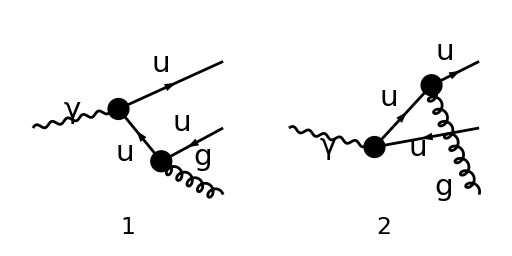

(64 π^2 α (N^2-1) e_Q^2 α_s (x1^2-ϵ (x1+x2-2)^2+x2^2))/((x1-1) (x2-1))

```mathematica
diags=InsertFields[CreateTopologies[0,1->3],{V[1]}->{F[3,{1}],-F[3,{1}],V[5]},InsertionLevel->{Classes},Model->"SMQCD"];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
RealEmissionMasslessDdimensional=(* Correct D-dimension photon spin averaging *)(2/(2-2ϵ)ComputeDiags[diags,D])/.{D->4-2ϵ}//Series[#,{ϵ,0,1}]&//Normal//FullSimplify
```

```mathematica
(RealEmissionMasslessDdimensional/BornMassless//FullSimplify)/.{SUNN->3}
```

-(32 π α_s (x1^2-ϵ (x1+x2-2)^2+x2^2))/(3 (ε-1) s (x1-1) (x2-1))

```mathematica
(
64 π^2 SMP["alpha_fs"]SMP["alpha_s"](SUNN^2 - 1) SMP["e_Q"]^2(((1-ϵ)(x1^2+x2^2)+2ϵ(1-x3))/((1-x1)(1-x2))-2ϵ)
-RealEmissionMasslessDdimensional
)/.{x3->2-x1-x2,SUNN->3}//FullSimplify
```

0

```mathematica
(
(RealEmissionMasslessDdimensional/BornMassless4D)/(((1-ϵ)(x1^2+x2^2)+2ϵ(1-x3))/((1-x1)(1-x2))-2ϵ)
)/.{x3->2-x1-x2,SUNN->3}//FullSimplify
```

(32 π α_s)/(3 s)

```mathematica
RealEmissionContrib=(Normal[FullSimplify[Series[Integrate[((1-ϵ)(x2^2+x1^2)+2ϵ (1-(2-x1-x2)))/((1-x1)^(1+ϵ)(1-x2)^(1+ϵ)(1-(2-x1-x2))^ϵ)-2ϵ,{x1,0,1},{x2,1-x1,1},Assumptions->{ϵ<0}],{ϵ,0,0}]]])/.{ϵ->Epsilon}
```

3/ε+2/ε^2-π^2+19/2

## Virtual cross-section

```mathematica
vamp=(1/ⅈ) FCFAConvert[
CreateFeynAmp[vdiags],
IncomingMomenta->{p},OutgoingMomenta->{k1,k2},LorentzIndexNames->{μ, ν, σ},SUNIndexNames->{_,_,_,a},SUNFIndexNames->{_,m,n,o},
LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,Prefactor->3/2 SMP["e_Q"],FinalSubstitutions->{SMP["m_e"]->0,SMP["m_u"]->0},DropSumOver->True
](*/.{Pair[__,Momentum[Polarization[__],_]]:>1}*)
```

(3 ⅈ e_Q g^νσ ε^μ(p) (φ(k1)).(-ⅈ γ^ν g_s T_mo^a).(γ·l).(-2/3 ⅈ e γ^μ).(γ·(-k1-k2+l)).(-ⅈ γ^σ g_s T_on^a).(φ(-k2)))/(32 π^4 l^2.(l-k1)^2.(-k1-k2+l)^2)

```mathematica
FCClearScalarProducts[];
ScalarProduct[k1,k1]=0;
ScalarProduct[k2,k2]=0;
ScalarProduct[p,p]=s;
ScalarProduct[k1,k2]=s/2;
```

```mathematica
(bornfcamp ComplexConjugate[bornfcamp])//SUNSimplify//DoPolarizationSums[#,p,0,VirtualBoson->True]&//FermionSpinSum//DiracSimplify//FeynAmpDenominatorExplicit//Simplify
```

2 (D-2) e^2 s C_A e_Q^2

```mathematica
bornfcamp
```

e e_Q δ_mn (φ(k1)).(γ·ε(p)).(φ(-k2))

```mathematica
vamp//SUNSimplify
```

-(e C_F e_Q g_s^2 g^νσ δ_mn ε^μ(p) (φ(k1)).γ^ν.(γ·l).γ^μ.(-(γ·(k1+k2-l))).γ^σ.(φ(-k2)))/(16 π^4 l^2.(k1-l)^2.(k1+k2-l)^2)

```mathematica
vampsq[0]=(((vamp) ComplexConjugate[bornfcamp]+bornfcamp ComplexConjugate[(vamp)])//SUNSimplify//DoPolarizationSums[#,p,0,VirtualBoson->True]&//FermionSpinSum//DiracSimplify//Simplify)/.{SMP["e"]^2 -> (4 Pi SMP["alpha_fs"])};
```

```mathematica
vampsq[0]
```

(α (D-2) C_A C_F e_Q^2 g_s^2 (2 (k1·l) ((D-4) s-4 (k2·l))+s (4 (k2·l)-(D-4) l^2)))/(π^3 l^2.(k1-l)^2.(k1+k2-l)^2)

```mathematica
vampsq[1]=TID[vampsq[0],l,(*UsePaVeBasis->True,PaVeAutoReduce->False,*)ToPaVe->True]
```

-(ⅈ α (2-D) (7-D) s C_A C_F e_Q^2 g_s^2 B_0(s,0,0))/π-(2 ⅈ α (2-D) s^2 C_A C_F e_Q^2 g_s^2 C_0(0,0,s,0,0,0))/π

```mathematica
vampsq[2]=PaXEvaluate[vampsq[1],PaXSimplifyEpsilon->False]
```

-(2 ⅈ α s C_A C_F e_Q^2 g_s^2 (-2 log(-μ^2/s)+2 ℽ-1-2 log(4 π)+4 log(2 π)))/(π ε)+(4 ⅈ α s C_A C_F e_Q^2 g_s^2)/(π ε^2)-1/(3 π)ⅈ α s C_A C_F e_Q^2 g_s^2 (-6 log^2(-μ^2/s)-12 log(4 π) log(-μ^2/s)+24 log(2 π) log(-μ^2/s)+12 ℽ log(-μ^2/s)-6 log(-μ^2/s)+π^2-6 ℽ^2+6 ℽ-30-6 log^2(4 π)-24 log^2(2 π)+24 log(2 π) log(4 π)+12 ℽ log(4 π)-6 log(4 π)-24 ℽ log(2 π)+12 log(2 π))

```mathematica
vampsq[2]=Normal[(FullSimplify[Series[(
(1/((SMP["alpha_s"]/(2π)CF )BornMassless)DiracSimplify[Normal[Series[
(Gamma[1-Epsilon]^2/Gamma[1-3Epsilon])^1(* Add normalization of the 1->3 d-dimensional volume factor *)
(1/Gamma[1-Epsilon])^-1(* Remove normalization of the 1->2 d-dimensional volume factor *)
(-s/(4π ScaleMu^2))^Epsilon(* Force factorization of the MSbar scale with s *)
(
(ⅈ Gamma[1-Epsilon]/(2π)^(-2Epsilon)(* Normalization of PaXEvaluate*))PaXEvaluate[vampsq[1],PaXSimplifyEpsilon->False]
)
,{Epsilon,0,0}]]])
/.{SMP["g_s"]->Sqrt[4 Pi SMP["alpha_s"]],CA->3}
),{Epsilon,0,0}],Assumptions->{ScaleMu>0,s<0}]
/.{
Log[-1/s]^2->Log[s]^2-π^2,
Log[-s]^2->Log[s]^2-π^2
}
)]
```

-3/ε-2/ε^2+π^2-8

## NLORratio

```mathematica
RealEmissionContrib
```

3/ε+2/ε^2-π^2+19/2

```mathematica
vampsq[2]
```

-3/ε-2/ε^2+π^2-8

```mathematica
RratioNLO=Subscript[R, Born](1+SMP["alpha_s"]/(2π)CF Simplify[RealEmissionContrib+vampsq[2]])/.{CF->4/3}
```

R_Born (α_s/π+1)